## New

```mathematica
MM=3;NN=2;
(B=RandomInteger[{1,1000},{MM,NN}])//TableForm
B[[3,1]]
Log@N@Sum[B[[i,NN]]/Sum[B[[i,j]],{j,1,NN}],{i,1,MM}]
```

301 | 900
948 | 156
111 | 171

111

0.403505

/Users/masteranza/Projects/MasterThesis/Work/Poster/

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]];
```

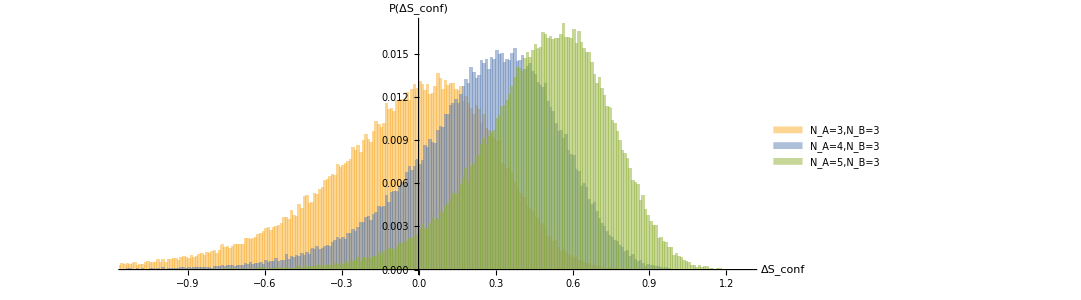

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure2.eps

```mathematica
H=Histogram[{DeltaS[3,3],DeltaS[4,3],DeltaS[5,3]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=3,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=4,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure2.eps",H]
```

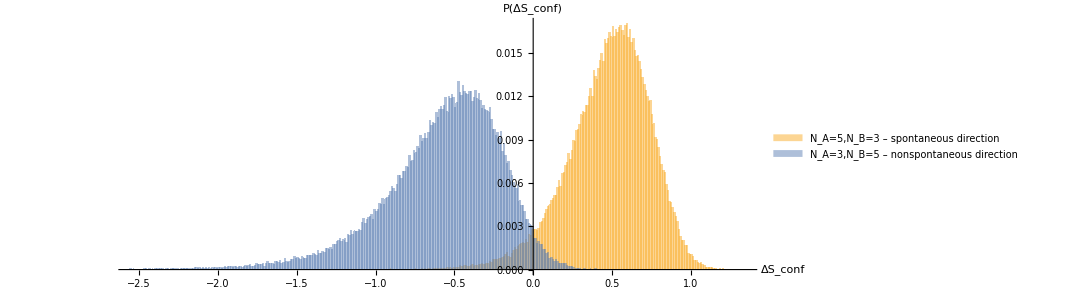

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure3.eps

```mathematica
H=Histogram[{DeltaS[5,3],DeltaS[3,5]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=5,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=5 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure3.eps",H]
```

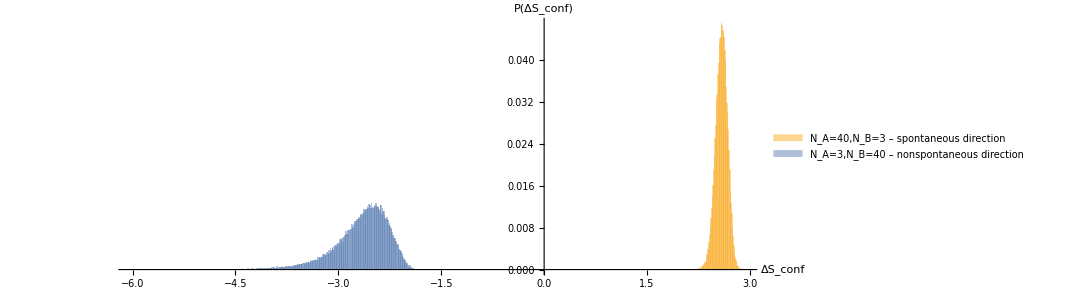

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure4.eps

```mathematica
H=Histogram[{DeltaS[40,3],DeltaS[3,40]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=40,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=40 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=40,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure4.eps",H]
```

## Poisson New

```mathematica
DeltaS[m_,n_]:=Table[{B=Table[RandomVariate[PoissonDistribution[500],n],m],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]];
```

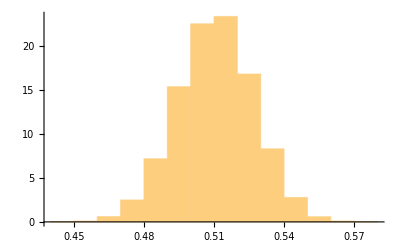

```mathematica
Histogram[DeltaS[5,3],{0.01},"PDF"]
```

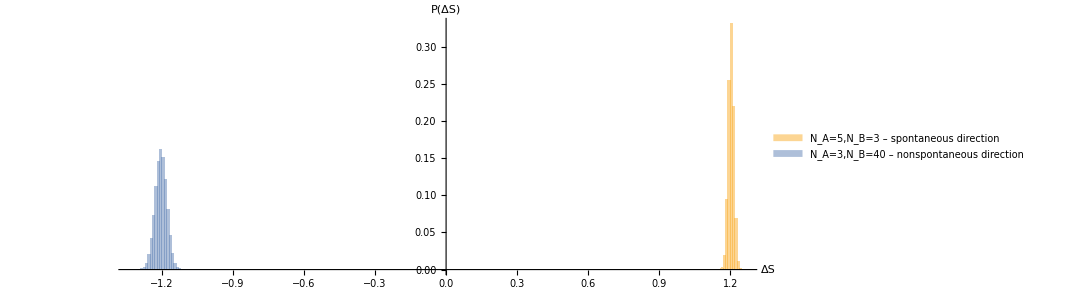

```mathematica
H=Histogram[{DeltaS[10,3],DeltaS[3,10]},{0.01},"Probability",AxesLabel->{Style["ΔS",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=40,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=40 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=40,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```